User - FRR Calculations

```mathematica
sol = Solve[a*x^2+b*x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
u1 = x /.sol[[2]]
```

(-b+√(b^2-4 a c))/(2 a)

```mathematica
u2=x /. sol[[1]]
```

(-b-√(b^2-4 a c))/(2 a)

```mathematica
ctag =Solve[Integrate[a*x^2+b*x+c,{x,u1,u2}]==1,c]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{c→(-6^(2/3) a^(4/3)+b^2)/(4 a)},{c→(-3 ⅈ 2^(2/3) 3^(1/6) a^(4/3)+6^(2/3) a^(4/3)+2 b^2)/(8 a)},{c→(3 ⅈ 2^(2/3) 3^(1/6) a^(4/3)+6^(2/3) a^(4/3)+2 b^2)/(8 a)}}

```mathematica
creal=c /. ctag[[1]]
```

(-6^(2/3) a^(4/3)+b^2)/(4 a)

```mathematica
FRR = Integrate[a*x^2+b*x+c,{x,u1,T}]
```

c (-(-b+√(b^2-4 a c))/(2 a)+T)+b (-((-b+√(b^2-4 a c))^2)/(8 a^2)+T^2/2)+a (-((-b+√(b^2-4 a c))^3)/(24 a^3)+T^3/3)

```mathematica
a=-2
b=4
c = N[(-(6^2*2^4)^(1/3)+16)/-8]
FRRN = Integrate[a*x^2+b*x+c,{x,u1,T}]
```

-2

4

-0.959958

-0.959958 (-0.278875+T)+4 (-0.0388857+T^2/2)-2 (-0.0072295+T^3/3)

Attacker Calculations

```mathematica
solAttacker = Solve[d*x^2+e*x+f==0,x]
```

{{x→(-e-√(e^2-4 d f))/(2 d)},{x→(-e+√(e^2-4 d f))/(2 d)}}

```mathematica
a1 = x /. solAttacker[[2]]
```

(-e+√(e^2-4 d f))/(2 d)

```mathematica
a2 = x/. solAttacker[[1]]
```

(-e-√(e^2-4 d f))/(2 d)

```mathematica
ftag =Solve[Integrate[d*x^2+e*x+f,{x,a1,a2}]==1,f]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{f→(-6^(2/3) d^(4/3)+e^2)/(4 d)},{f→(-3 ⅈ 2^(2/3) 3^(1/6) d^(4/3)+6^(2/3) d^(4/3)+2 e^2)/(8 d)},{f→(3 ⅈ 2^(2/3) 3^(1/6) d^(4/3)+6^(2/3) d^(4/3)+2 e^2)/(8 d)}}

```mathematica
freal = f /.ftag[[1]]
```

(-6^(2/3) d^(4/3)+e^2)/(4 d)

```mathematica
FAR=Integrate[d*x^2+e*x+f,{x,T,a2}]
```

f ((-e-√(e^2-4 d f))/(2 d)-T)+e (((-e-√(e^2-4 d f))^2)/(8 d^2)-T^2/2)+d (((-e-√(e^2-4 d f))^3)/(24 d^3)-T^3/3)

```mathematica
d = -1
e = 4
f= N[(-(6^2*(1)^4)^(1/3)+(4)^2)/(-4*(1))]
FARN=Integrate[d*x^2+e*x+f,{x,T,a2}]
```

-1

4

-3.17452

-8.20187-3.17452 (2.90856-T)+T^3/3+4 (4.22986-T^2/2)

Safe Functions

```mathematica
SafePDF= 1-FRR-FAR+FAR*FRR
```

9.20187+3.17452 (2.90856-T)+0.959958 (-0.278875+T)-T^3/3-4 (4.22986-T^2/2)-4 (-0.0388857+T^2/2)+2 (-0.0072295+T^3/3)+(-8.20187-3.17452 (2.90856-T)+T^3/3+4 (4.22986-T^2/2)) (-0.959958 (-0.278875+T)+4 (-0.0388857+T^2/2)-2 (-0.0072295+T^3/3))

```mathematica
safe=FullSimplify[SafePDF]
```

1.32378-0.222222 T (5.9289+T (19.4943+T (-40.4473+T (28.9635+(-9.+T) T))))

```mathematica
Collect[safe,T]
```

1.32378-1.31753 T-4.33206 T^2+8.9883 T^3-6.43633 T^4+2. T^5-0.222222 T^6

```mathematica
dev = D[safe,T]
```

-0.222222 T (19.4943+T (-40.4473+T (28.9635+(-9.+T) T))+T (-40.4473+T (28.9635+(-9.+T) T)+T (28.9635+(-9.+T) T+T (-9.+2 T))))-0.222222 (5.9289+T (19.4943+T (-40.4473+T (28.9635+(-9.+T) T))))

```mathematica
eq=Collect[dev,T]
```

-1.31753-8.66412 T+26.9649 T^2-25.7453 T^3+10. T^4-1.33333 T^5

```mathematica
crit=Reduce[eq==0,T]
```

T==-0.110157||T==1.09144||T==1.40937||T==1.72112||T==3.38822

```mathematica
secondDev=D[safe,{T,2}]
```

0.-0.222222 T (T (T (2 T+2 (-9.+2 T))+2 (28.9635+(-9.+T) T+T (-9.+2 T)))+2 (-40.4473+T (28.9635+(-9.+T) T)+T (28.9635+(-9.+T) T+T (-9.+2 T))))-0.444444 (19.4943+T (-40.4473+T (28.9635+(-9.+T) T))+T (-40.4473+T (28.9635+(-9.+T) T)+T (28.9635+(-9.+T) T+T (-9.+2 T))))

```mathematica
solutions=List@@crit
```

{T==-0.110157,T==1.09144,T==1.40937,T==1.72112,T==3.38822}

```mathematica
exprs=Replace[solutions,T==val_:>val,{1}]
```

{-0.110157,1.09144,1.40937,1.72112,3.38822}

```mathematica
Table[{val,Sign[secondDev/. T->val]},{val,exprs}]
```

{{-0.110157,-1},{1.09144,1},{1.40937,-1},{1.72112,1},{3.38822,-1}}

```mathematica
Tmin=Max[a1,u1]
Tmax=Min[a2,u2]
```

1.09144

1.72112

```mathematica
maxPoints=Select[exprs,(Sign[secondDev/. T->#]==-1)&& Tmin<=#<=Tmax&];
valuesAtMax=Table[{t,safe/. T->t},{t,maxPoints}]
globalMax=MaximalBy[valuesAtMax,Last]
globalMax=First[globalMax]
```

{{1.40937,0.00973287}}

{{1.40937,0.00973287}}

{1.40937,0.00973287}

Find EER

```mathematica
EER = Reduce[FAR==FRR,T]
```

T==0.187919||T==1.44249||T==2.36959

```mathematica
T==(b+e)/4||T==1/4 (b+e-√3 √(-4 (-1)^(1/3) 6^(2/3)-b^2+2 b e-e^2))||T==1/4 (b+e+√3 √(-4 (-1)^(1/3) 6^(2/3)-b^2+2 b e-e^2))
```

T==15/4||T==1/4 (15-√(3 (-25-4 (-1)^(1/3) 6^(2/3))))||T==1/4 (15+√(3 (-25-4 (-1)^(1/3) 6^(2/3))))

```mathematica
sol=List@@EER
eerVals=Replace[solutions,T==val_:>val,{1}]
validEERVals=Select[eerVals,Tmin<=#<=Tmax&]
safeVals=(safe/. T->#)&/@validEERVals
eerSafePairs=Transpose[{validEERVals,safeVals}]
maxEERPair=MaximalBy[eerSafePairs,Last][[1]]
```

{T==0.187919,T==1.44249,T==2.36959}

{0.187919,1.44249,2.36959}

{1.44249}

{0.00951573}

{{1.44249,0.00951573}}

{1.44249,0.00951573}

Safe Plot

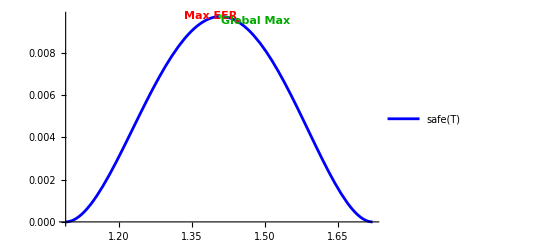

```mathematica
Show[Plot[safe,{T,Tmin,Tmax},PlotStyle->Blue,PlotLegends->{"safe(T)"}],Graphics[{Red,PointSize[Large],Point[maxEERPair],Text[Style["Max EER",Red,Bold],maxEERPair,{1,-1}],Green,PointSize[Large],Point[globalMax],Text[Style["Global Max",Darker[Green],Bold],globalMax,{-1,1}]}]]
```

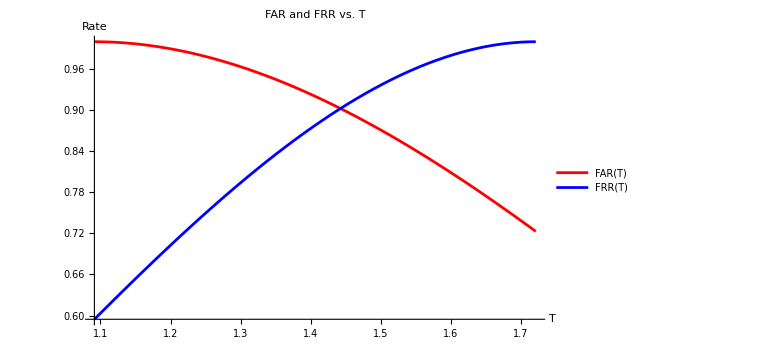

```mathematica
Plot[{FAR,FRR},{T,Tmin,Tmax},PlotStyle->{Red,Blue},PlotLegends->{"FAR(T)","FRR(T)"},PlotLabel->"FAR and FRR vs. T",AxesLabel->{"T","Rate"},PlotRange->All,ImageSize->Large]
```

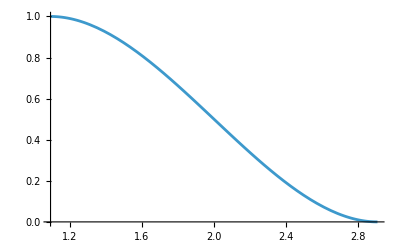

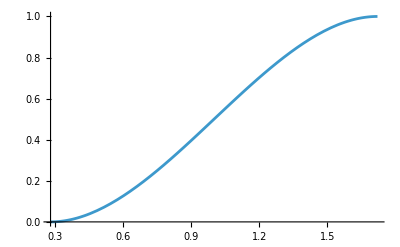

```mathematica
Plot[FAR,{T,a1,a2}]
Plot[FRR,{T,u1,u2}]
```

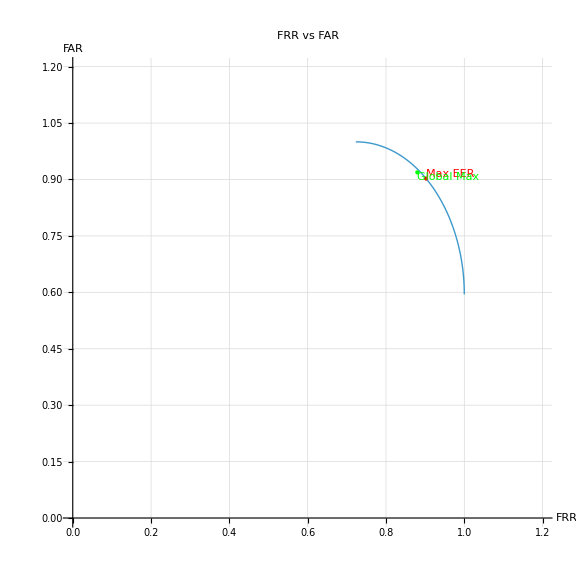

```mathematica
ParametricPlot[{FAR,FRR},{T,Tmin,Tmax},PlotStyle->Thick,AxesLabel->{"FRR","FAR"},PlotLabel->"FRR vs FAR",PlotRange->{{0,1.2},{0,1.2}},ImageSize->Large,GridLines->Automatic,Epilog->{Red,PointSize[Large],Point[{FRR/. T->maxEERPair[[1]],FAR/. T->maxEERPair[[1]]}],Text["Max EER",{FRR/. T->maxEERPair[[1]],FAR/. T->maxEERPair[[1]]},{-1,-1}],Green,PointSize[Large],Point[{FRR/. T->globalMax[[1]],FAR/. T->globalMax[[1]]}],Text["Global Max",{FRR/. T->globalMax[[1]],FAR/. T->globalMax[[1]]},{-1,1}]}]
```